## Painting dipole trap

### Simple Harmonic potential

We can simply solve the equation for the beam position f(t) as a function of

```mathematica
eqn = Integrate[(1-x^2),{x,-f[t],f[t]}]==t
```

2 f[t]-(2 f[t]^3)/3==t

```mathematica
sol = DSolve[eqn,f[t],t,Assumptions->{-1<=f[t]<=1,t ∈ Reals,f[t]∈Reals}]
```

{{f[t]→-2^(2/3)/((3 t+√(-16+9 t^2))^(1/3))-((3 t+√(-16+9 t^2))^(1/3))/2^(2/3)},{f[t]→(1+ⅈ √3)/(2^(1/3) (3 t+√(-16+9 t^2))^(1/3))+((1-ⅈ √3) (3 t+√(-16+9 t^2))^(1/3))/(2 2^(2/3))},{f[t]→(1-ⅈ √3)/(2^(1/3) (3 t+√(-16+9 t^2))^(1/3))+((1+ⅈ √3) (3 t+√(-16+9 t^2))^(1/3))/(2 2^(2/3))}}

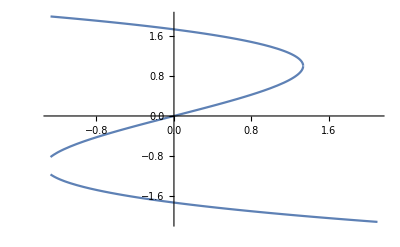

```mathematica
Plot[f[t]/.sol,{t,-4/Pi,2+0.1}]
```

```mathematica
2/Pi
```

2/π

```mathematica
N[2/π]
```

0.63662

```mathematica
Solve[(f[t]/.sol[[1]])==1,t]
```

ReplaceAll::reps: {1} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→f^(-1)[InverseFunction[ReplaceAll,1,2][1,1]]}}